## Invierte audio

Reproduce el audio en el orden inverso.

```mathematica
Args[f_]:= Apply[List,f];
InvertMidi[audio_]:=Module[{midi,last,newmidi,a},
midi = Map[Args,audio[[1]]];
last = Max[Flatten[midi[[All,2]]]];
newmidi = midi;
newmidi[[All,2]] = last-newmidi[[All,2]];
a = Transpose[newmidi[[All,2]]];
newmidi[[All,2]] = Transpose[{a[[2]],a[[1]]}];
Return[Reverse[Table[Apply[SoundNote,i],{i,newmidi}]]];
];
```

```mathematica
audio = Import[NotebookDirectory[]<>"ballade1.mid"];
Sound[InvertMidi[audio]]
```

## Cambia tono

```mathematica
StringToPitch[string_String]:=Module[{noteValues,noteList,pitch},
noteValues={"C","C#","D","D#","E","F","F#","G","G#","A","A#","B"};
noteList=StringCases[string,{RegularExpression["[A-G]#?"],RegularExpression["\\d+"]}];
pitch=Position[noteValues,First[noteList]][[1,1]]-1;
((ToExpression[noteList[[2]]]-4)*12)+pitch
];
Args[f_]:= Apply[List,f];
ChangePitch[audio_,pitchchage_]:= Module[{midi,timing,newmidi,pitches},
midi = Map[Args,audio[[1]]];
pitches = Map[StringToPitch,midi[[All,1]]];
pitches += pitchchage;
newmidi = midi;
newmidi[[All,1]] = pitches;
Return[Table[Apply[SoundNote,i],{i,newmidi}]];
];
```

```mathematica
audio = Import[NotebookDirectory[]<>"ballade1.mid"];
Sound[ChangePitch[audio,2]]
```

## Modifica tiempos

Introduce pequeñas variaciones en el tiempo de ejecución de las notas.

```mathematica
Args[f_]:= Apply[List,f];
RandomTimeChange[audio_,dist_:UniformDistribution[{-0.01,0.01}]]:= Module[{midi,timing,newmidi},
midi = Map[Args,audio[[1]]];
timing = Table[i[[2]]+{RandomVariate[dist],RandomVariate[dist]},{i,midi}];
newmidi = midi;
newmidi[[All,2]] = timing;
Return[Table[Apply[SoundNote,i],{i,newmidi}]];
];
```

```mathematica
audio = Import[NotebookDirectory[]<>"ballade1.mid"];
Sound[RandomTimeChange[audio,NormalDistribution[0,0.01]]]
```

## Espectro de notas

Convirtiendo todas las notas a sus valores midi, [0,127], se puede hacer el histograma de frecuencias.

```mathematica
StringToPitch[string_String]:=Module[{noteValues,noteList,pitch},
noteValues={"C","C#","D","D#","E","F","F#","G","G#","A","A#","B"};
noteList=StringCases[string,{RegularExpression["[A-G]#?"],RegularExpression["\\d+"]}];
pitch=Position[noteValues,First[noteList]][[1,1]]-1;
((ToExpression[noteList[[2]]]-4)*12)+pitch
];
Args[f_]:= Apply[List,f];
SetOptions[{Histogram,Plot,ListPlot,DiscretePlot},BaseStyle->FontSize->14];
MidiHistogram[audio_Sound,title_:""]:=Module[{midi,numnotes},
midi = Map[Args,audio[[1]]];
numnotes = Map[StringToPitch,midi[[All,1]]]+60;
Print[Histogram[numnotes,Automatic,"Probability",PlotTheme->"Scientific",FrameLabel->{"Nota","Probabilidad"},PlotLabel->title]];
];
MidiEntropy[audio_]:= N[Entropy[audio[[1,All,1]]]];
```

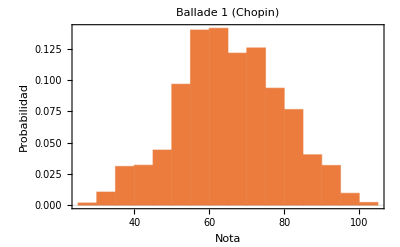

```mathematica
audio = Import[NotebookDirectory[]<>"ballade1.mid"];
MidiHistogram[audio, "Ballade 1 (Chopin)"]
```

```mathematica
MidiEntropy[audio]
```

3.92924

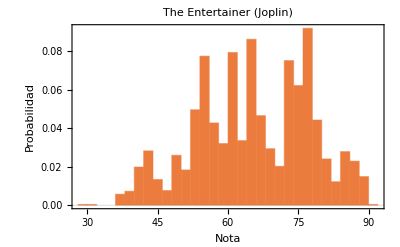

```mathematica
audio = Import[NotebookDirectory[]<>"entertainer.mid"];
MidiHistogram[audio, "The Entertainer (Joplin)"]
```

```mathematica
MidiEntropy[audio]
```

3.4942

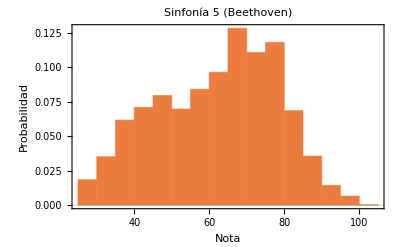

```mathematica
audio = Import[NotebookDirectory[]<>"symphony5_1.mid"];
MidiHistogram[audio, "Sinfonía 5 (Beethoven)"]
```

```mathematica
MidiEntropy[audio]
```

3.92433

## Sintetizador (cambiar afinación)

El sintetizador funciona superponendo ondas con la forma waveform, en una tabla discreta con frecuencia de sampleo 44100, y posteriormente se genera el audio a partir de esta tabla. Como argumento se pasan las notas en convención midi, es decir valores de 0 a 127. La afinación del sintetizador se puede especificar en tuning.

```mathematica
(* Crea tabla de audio que se va a sintetizar. *)
CreateSoundTable[length_,waveform_:Sin]:=(
samplerate=44100;
timelength = Ceiling[length];
notefc = N[(2 π)/samplerate];
notefunc = Compile[{{t,_Real}},waveform[notefc*t]];
finalSound = ConstantArray[0,{timelength*samplerate}];
);

(* Convierte notas musicales (texto) a valores numéricos. *)
StringToPitch[string_String]:=Module[{noteValues,noteList,pitch},
noteValues={"C","C#","D","D#","E","F","F#","G","G#","A","A#","B"};
noteList=StringCases[string,{RegularExpression["[A-G]#?"],RegularExpression["\\d+"]}];
pitch=Position[noteValues,First[noteList]][[1,1]]-1;
((ToExpression[noteList[[2]]]-4)*12)+pitch
];

(* Extrae los argumentos de una función. *)
Args[f_]:= Apply[List,f];

(* Formatea la entrada en formato Midi al formato de entrada del sintetizador. *)
SynthFormat[audio_Sound,takenotes_:-1]:=Module[{midi,notes},
If[takenotes ≠ -1,
notes = audio[[1,1;;takenotes]];,
notes = audio[[1]];
];
midi = Map[Args,notes];
midi[[All,1]] = Map[StringToPitch, midi[[All,1]]]+60;
midi[[All,4]] = midi[[All,4,2]];
midi = midi[[All,{1,2,4}]];
Return[midi];
];
SynthFormat[audio_List]:=Module[{midi,notes},
midi = Map[Args,audio];
midi[[All,1]] = Map[StringToPitch, midi[[All,1]]]+60;
midi[[All,4]] = midi[[All,4,2]];
midi = midi[[All,{1,2,4}]];
Return[midi];
];

(* Añade nota al audio. *)
AddNote[freq_,{init_,end_},volume_]:=Module[{initPos, endPos},
initPos = Floor[init*samplerate]+1;
endPos = Floor[end*samplerate]+1;
finalSound[[initPos;;endPos]] += Table[notefunc[freq*t],{t,initPos,endPos}];
];

(* Proceso para generar la señal. *)
SynthAudio[audio_,tuning_,waveform_:Sin]:=Module[{maxtime},
maxtime = Max[Flatten[audio[[All,2]]]];
CreateSoundTable[maxtime,waveform];
Monitor[
i=1;
SetSharedVariable[i,finalSound];
Do[
i++;
AddNote[tuning[noteparam[[1]]],noteparam[[2]],noteparam[[3]]];
,{noteparam,audio}
];,
Row[{ProgressIndicator[i,{1,Length[audio]}],i}," "]
];
Return[SampledSoundList[finalSound,samplerate]];
];

(* Afinaciones. *)
StdTuning[mn_Integer]:= N[440 2^((mn-69)/12)];
Son13Tuning[mn_Integer]:= N[440 2^((mn-69)/13)];
PythagoreanTuning[x_Integer]:=440 Power[3/2,Mod[(x-69)*7,12]]*Power[.5,Floor[(Mod[(x-69)*7,12]*7)/12]]*Power[2,Floor[(x-69)/12]] ;
eTuning[mn_Integer]:= N[440 ⅇ^((mn-69)/12)];
JustHold={1,16/15,9/8,6/5,5/4,4/3,45/32,3/2,8/5,5/3,16/9,15/8};
JustTuning[x_Integer]:=440JustHold[[Mod[(x-69),12]+1]]*Power[2,Floor[(x-69)/12]];

(* Forma de onda. *)
π2 = 2 π;
NoteSawtooth[x_]:= 2SawtoothWave[x/π2]-1;
NoteSquareWave[x_]:=SquareWave[x/π2];
NoteTriangle[x_]:=TriangleWave[x/π2];
```

### Gráficas de afinación

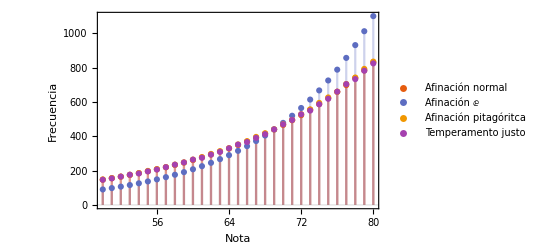

```mathematica
SetOptions[{Histogram,Plot,ListPlot,DiscretePlot},BaseStyle->FontSize->14];
DiscretePlot[{StdTuning[x],eTuning[x],PythagoreanTuning[x],JustTuning[x]},{x,50,80}, PlotTheme->"Scientific",FrameLabel->{"Nota","Frecuencia"},PlotLegends->{"Afinación normal", "Afinación ⅇ","Afinación pitagóritca","Temperamento justo"}]
```

### Audio sintetizado

Escala Do mayor

```mathematica
audio = Import[NotebookDirectory[]<>"c_major.mid"];
ret = SynthAudio[SynthFormat[audio],StdTuning,NoteTriangle];
Sound[ret]
```

```mathematica
ret = SynthAudio[SynthFormat[audio],Son13Tuning,NoteTriangle];
Sound[ret]
```

Ballade 1, Chopin

```mathematica
audio = Import[NotebookDirectory[]<>"ballade1.mid"];
```

```mathematica
ret = SynthAudio[SynthFormat[audio,800],StdTuning,NoteSawtooth];
```

```mathematica
Sound[ret]
```

Con otra afinación

```mathematica
audio = Import[NotebookDirectory[]<>"ballade1.mid"];
ret = SynthAudio[SynthFormat[audio,1000],Son13Tuning,NoteTriangle];
Sound[ret]
```